```mathematica
littlewood[n_Integer,x_:x]:=1+Tuples[{1,-1},n]. x^Range[n]
```

```mathematica
littlewood[3]//Column//TraditionalForm
```

x^3+x^2+x+1
-x^3+x^2+x+1
x^3-x^2+x+1
-x^3-x^2+x+1
x^3+x^2-x+1
-x^3+x^2-x+1
x^3-x^2-x+1
-x^3-x^2-x+1

```mathematica
littlewoodRoots[n_]:= ComplexListPlot[x/. Solve[Times @@ littlewood[n]==0, x]]
```

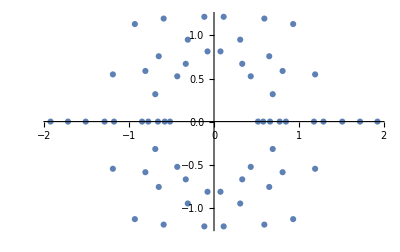

```mathematica
littlewoodRoots[4]
```

#### A fancier function with a slight increase in speed:

```mathematica
polynomialRoots[n_Integer,x_:Unique[],graph_:0]:=With[{
map=If[n>5,ParallelMap,Map],
solve=If[$VersionNumber<12.3,x/. NSolve@##&,NSolveValues],
break=If[TrueQ@graph,ReIm,Identity],
mirror=If[n>3,Thread,Identity]@Join[#,-#]&,
poly=1+#+Tuples[{1,-1},n-1]. #^Range[2,n]&},
If[map===ParallelMap && $KernelCount<2$ProcessorCount,
LaunchKernels[2$ProcessorCount-$KernelCount]];
map[break@solve[#==0,x]&,poly@x]//mirror]
```

```mathematica
Block[{r,k=4-$KernelCount},If[k>0,LaunchKernels@k];
AbsoluteTiming[r=fastRootCalculate[10];]]
```

{0.428502,Null}

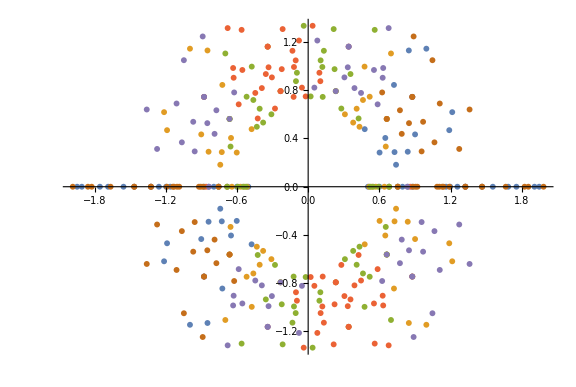

```mathematica
ComplexListPlot[fastRootCalculate[6],ImageSize->Large]
```

```mathematica
displayRoots[n_]:=With[{
m=If[n>5,1,40/(n+7)],
g=Sequence@@{#3[[#]],Hue[#/n],Point@#2[[#]]}&,
d=8.2 {#,#} 2^-{2,5/2}&[{-1,1}],
o=Tr@Range[14-n]+3Clip[8.2-n/2]/2+5/2},
With[{
w=ImageSize->5000/m,r=PlotRange->d,
a=AspectRatio->Tr@Ratios[Differences/@d],
l=PlotLabel->Style[Row@{"n = ",n},FontSize->120/m],
s=AbsolutePointSize/@Table[o/m,n]~Riffle~If[n==18,2,o/m],
p=polynomialRoots[n,Unique[],m==1]},
If[m==1,
Graphics[g[#,p,s]&~ParallelArray~n,w,r,l],
ComplexListPlot[p,PlotStyle->Last@s,a,w,r,l]~Magnify~m]]
]
```

```mathematica
Block[{n=18,t,a=AbsoluteTiming,g="1.png",k},
k=2 $ProcessorCount-$KernelCount;
If[k>0,LaunchKernels@k];
Print["Testing process for: n = "<>ToString@n];
t=First/@{
a[k=displayRoots[1];],
a[k=Rasterize[k,"Image",Background->None];],
a[Export[g,k];k={0,0};DeleteFile[g];],k};
t[[-1]]=First@a[k=fastRootCalculate@n;];
Column@Prepend[{t},"Timing Values (sec):"]]
```

Testing process for: n = 18

Timing Values (sec):
{0.236715,2.93841,1.64122,150.978}

```mathematica
Block[{t=Table[{0,0},20],g="r-output",a=AbsoluteTiming,f},
f=2$ProcessorCount-$KernelCount;
If[f>0,LaunchKernels@f;Pause@1];
CreateDirectory[g]//Quiet;
f=Array[FileNameJoin[{g,ToString@#<>".png"}]&,Length@t];
Do[Print[Row@{"Calculating roots: n = ",i}~Style~Red];
t[[i]]=First/@{
a[g=displayRoots[i];Print["Rendering: "<>f[[i]]];],
a[Export[f[[i]],g,Background->None];]},
{i,Length@t}];
g={n,"Calculations","Graphics & Saving"};
Print["Done!"];CloseKernels[];
a=First/@{
a[CreateArchive[f,"littlewood.zip",OverwriteTarget->True];],
a[f=Import/@f;],
a[Export["littlewood.gif",f,"DisplayDurations"->3/2];]};
f={"Create Archive","Import Files","Make gif"};
Column@Riffle[Table[" ",4],{
Style["Timing Values (sec):",FontSize->14,FontWeight->Bold],
TableForm[MapIndexed[#2~Join~#1&,t],TableHeadings->{None,g}],
Style["Finalize & publish the results:",FontSize->14],
TableForm[{a},TableHeadings->{None,f}]}]
]
```

Timing Values (sec):
 
n | Calculations | Graphics & Saving
1 | 0.046781 | 1.77464
2 | 0.927909 | 1.74585
3 | 0.142804 | 1.7641
4 | 0.0328558 | 1.76063
5 | 0.10154 | 1.91935
6 | 0.148467 | 1.8114
7 | 0.0951283 | 1.79821
8 | 0.123576 | 1.83058
9 | 0.264738 | 1.93567
10 | 0.458345 | 2.14698
11 | 0.98753 | 2.59227
12 | 1.85967 | 3.34905
13 | 3.86464 | 5.0165
14 | 8.06182 | 8.07281
15 | 16.7945 | 15.2827
16 | 35.0206 | 28.8745
17 | 72.8436 | 58.4804
18 | 151.734 | 96.6706
19 | 321.23 | 190.365
20 | 668.058 | 419.341
 
Finalize & publish the results:
 
Create Archive | Import Files | Make gif
4.40382 | 9.89528 | 32.0446